### Reproduksi hasil Ho dan Matsuo

#### Hitung exterior

```mathematica
Clear["Global`*"];
pers1:=κ P0[rs] r[rs]^2 Exp[ρ[rs]]+2r[rs] r''[rs]-4r[rs]r'[rs] ρ'[rs]+2α ρ''[rs]-2α ρ'[rs]^2
pers2:=2Exp[2ρ[rs]]+κ(P0[rs] Exp[ρ[rs]]-2 m0[rs] Exp[2ρ[rs]])r[rs]^2-2r[rs] r''[rs]-2 r'[rs]^2-2α ρ''[rs]

α=5.* 10.^-2;
κ =1;
a0:=10.
rs00:=300.
rs0:=-60.
m00:=25.2
R=x/.Solve[rs00==x+a0 Log[x/a0-1],x][[1]];
r0=R+a0 Log[R/a0-1];
rn=-1.*10.^3;
ρ0=1/2 Log[1-a0/R];
ρ01=1/2 a0/R^2;
m0[rs_]=Piecewise[{{0./κ,rs>y},{m00/κ,rs≤y}}]/.{y->rs0}
P0[rs_]=Piecewise[{{0./κ,rs>y},{m0[rs] Exp[ρ0],rs≤y}}]/.{y->rs0}
N[{κ m0[rs],r0,a0,α}]
(*N[{r0,rn,a0/R,a0/x}/.Solve[-60.==x+a0 Log[x/a0-1],x][[1]]]
N[{ρ[r0]==ρ0,ρ'[r0]==ρ01,r[r0]==R,r'[r0]==(1-a0/R)}]*)
```

Piecewise[{{0., rs>-60.}, {25.2, rs≤-60.}, {0, True}}]

Piecewise[{{0., rs>-60.}, {0.981131 (Piecewise[{{0., rs>-60.}, {25.2, rs≤-60.}, {0, True}}]), rs≤-60.}, {0, True}}]

{Piecewise[{{0., rs>-60.}, {25.2, rs≤-60.}, {0., True}}],300.,10.,0.05}

```mathematica
s=NDSolve[{pers1+pers2==0,pers1-pers2==0,ρ[r0]==ρ0,ρ'[r0]==ρ01,r[r0]==R,r'[r0]==(1-a0/R)},{ρ,r},{rs,rs00,rn}]
ρo[rs_]=Evaluate[ρ[rs]/.s][[1]];
ro[rs_]=Evaluate[r[rs]/.s][[1]];
```

{{ρ→InterpolatingFunction[{{-60., 300.}}, <>],r→InterpolatingFunction[{{-60., 300.}}, <>]}}

#### Hitung interior

```mathematica
pers1:=κ P0[rs] r[rs]^2 Exp[ρ[rs]]+2r[rs] r''[rs]-4r[rs]r'[rs] ρ'[rs]+2α ρ''[rs]-2α ρ'[rs]^2
pers2:=2Exp[2ρ[rs]]+κ(P0[rs] Exp[ρ[rs]]-2 m0[rs] Exp[2ρ[rs]])r[rs]^2-2r[rs] r''[rs]-2 r'[rs]^2-2α ρ''[rs]
R=x/.Solve[rs0==x+a0 Log[x/a0-1],x][[1]];
r0=R+a0 Log[R/a0-1];
rn=-1.*10.^3;

ρ0=ρo[rs0];
ρ01=ρo'[rs0];
m0[rs_]=Piecewise[{{0./κ,rs>y},{m00/κ,rs≤y}}]/.{y->rs0}
P0[rs_]=Piecewise[{{0./κ,rs>y},{m0[rs] Exp[ρ0],rs≤y}}]/.{y->rs0}
N[{κ m0[rs0],r0,a0,α}]
```

Piecewise[{{0., rs>-60.}, {25.2, rs≤-60.}, {0, True}}]

Piecewise[{{0., rs>-60.}, {0.00666856 (Piecewise[{{0., rs>-60.}, {25.2, rs≤-60.}, {0, True}}]), rs≤-60.}, {0, True}}]

{25.2,-60.,10.,0.05}

```mathematica
s2=NDSolve[{pers1+pers2==0,pers1-pers2==0,ρ[rs0]==ρ0,ρ'[rs0]==ρ01,r[rs0]==ro[rs0],r'[rs0]==ro'[rs0]},{ρ,r},{rs,rs0,rn}]
ρi[rs_]=Evaluate[ρ[rs]/.s2][[1]];
ri[rs_]=Evaluate[r[rs]/.s2][[1]];
```

{{ρ→InterpolatingFunction[{{-1000., -60.}}, <>],r→InterpolatingFunction[{{-1000., -60.}}, <>]}}

```mathematica
ρsol[rs_]:=Piecewise[{{ρo[rs],rs≥y},{ρi[rs],rs<y}}]/.{y->rs0}
rsol[rs_]:=Piecewise[{{ro[rs],rs≥y},{ri[rs],rs<y}}]/.{y->rs0}
```

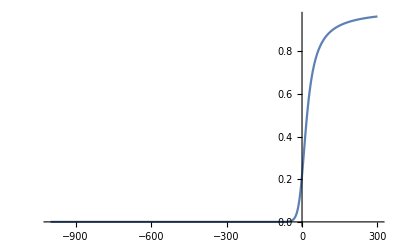

```mathematica
Plot[Exp[2ρsol[rs]],{rs,rn,rs00}]
```

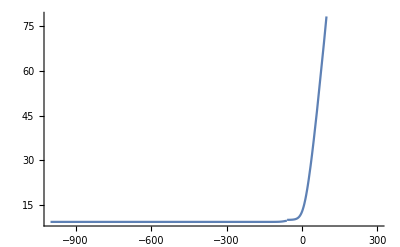

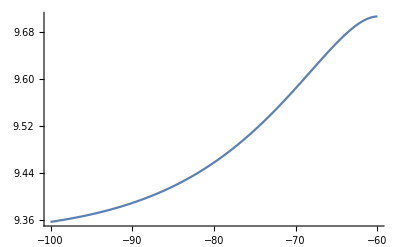

```mathematica
Plot[rsol[rs],{rs,rn,rs00}]
Plot[rsol[rs],{rs,-100,-60.}]
```

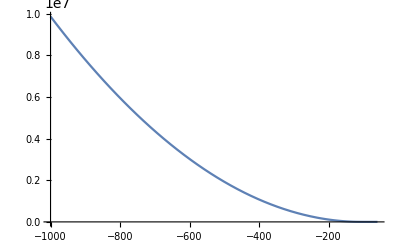

```mathematica
Psol[rs_]=-m0[rs0]+P0[rs0]Exp[-ρsol[rs]];
Plot[Psol[rs],{rs,rn,-60.}]
```